```mathematica
<<KPTools.m;
```

### Some integrals for the paper

```mathematica
Clear[y,β,τ];
Integrate[(1-Exp[-π y])^2/y^2,{y,0,β τ},Assumptions->{β>0,τ>0,τ β>1}]
```

-1/(β τ)+2 π -1π β τ-2 π -12 π β τ+π log(4)

```mathematica
Normal[Series[%,{β,∞,1}]]
```

π log(4)-1/(β τ)

```mathematica
Integrate[(1-cosθ^2)(1+((q-k cosθ)/ω)cosθ)+(1-cosθ^2)(1-((q-k cosθ)/ω)cosθ),{cosθ,-1,1}]
```

8/3

```mathematica
Simplify[Sqrt[1-cosθ^2]^3 (1+λ ((q-k cosθ)/ω) cosθ)//.{cosθ->Cos[θ],ω->Sqrt[k^2+q^2-2 k q cosθ]}]
Simplify[Series[%,{θ,0,3}],Assumptions->{θ>0}]
```

(sin^2(θ))^(3/2) ((λ cos(θ) (q-k cos(θ)))/(√(k^2-2 k q cos(θ)+q^2))+1)

(θ^3 (-k λ+√((k-q)^2)+λ q))/(√((k-q)^2))+O(θ^4)

```mathematica
II=Sqrt[1-cosθ^2]^3 (1+λ ((q-k cosθ)/ω) cosθ) Log[1-(I π β)/(ω-λ k+q)] Log[1+(I π β)/(ω-λ k+q)]/. {ω->Sqrt[k^2+q^2-2 k q cosθ]};
II=Simplify[II/.Log[X_]Log[Y_]:>Log[X Y]]
(*Integrate[%,{cosθ,-1,1}]*)
Integrate[II,{k,qmin,q}]
```

-((1-cosθ^2)^(3/2) (-√(k^2-2 k q cosθ+q^2)+k λ cosθ^2-λ q cosθ) log((π^2 β^2)/((√(k^2-2 k q cosθ+q^2)-k λ+q)^2)+1))/(√(k^2-2 k q cosθ+q^2))

∫_qmin^q -((1-cosθ^2)^(3/2) (-√(k^2-2 k q cosθ+q^2)+k λ cosθ^2-λ q cosθ) log((π^2 β^2)/((√(k^2-2 k q cosθ+q^2)-k λ+q)^2)+1))/(√(k^2-2 k q cosθ+q^2))ⅆk

```mathematica
(2 π^3 106.75)/270*(3.38/106.75)^(1/3)*100^4*1/(2.3*^-4)((3*^11GeV)^5)/(1/Sqrt[8π GN]^4)*1*^-6//.NN
```

0.232922

```mathematica
1*^11GeV/cm^3/(1*^-5Msun/pc^3)//.NN
```

2.62839×10^14

### Fermion Energy Density Today

```mathematica
(Hs^2 zs^2)/(3 MPl^2)
Hs^2/(3 MPl^2 as^2)==Hs^2/(3 MPl^2)1/Hs^2 1/(3 MPl^2)π^2/30 gs Ts^4==π^2/(270 MPl^4)gs Ts^4
```

```mathematica
π^2/270 gs Ts^4/MPl^4
```

```mathematica
Hs^2/as^2==1/(3 MPl^2)π^2/30 gs Ts^4
```

```mathematica
π^2/270 106.75^(4/3)/3.38^(1/3)100^4*1/(2.73Kelvin)*(((3.8*^11GeV)^5)/(1/Sqrt[8π GN]^4))*1*^-6//.NN
```

0.59039

### Integrals for incoherent GW backgrounds

#### Time integrals

```mathematica
(* incoherent GWs *)
$Assumptions={ττ>τs>0,0<τi<ττ,β>0};
II=Δη zs^2 Pgw Integrate[τs^2/τ^2(1-Exp[-π β τ])^2,{τ,0,∞}]
```

π β Δη Pgw τs^2 zs^2 log(4)

```mathematica
(* coherent GWs *)
$Assumptions={ϵ>0,β>0,q>k>0,ω>0,τ>τi>0};
Ia=Integrate[1/(τp-I ϵ)(1-Exp[-π β (τp-I ϵ)])Exp[I(k+ω+q)(τp-I ϵ)]/.ϵ->0,{τp,0,∞}]
```

log(-ⅈ (ⅈ π β+k+q+ω))-log(k+q+ω)+(ⅈ π)/2

```mathematica
FullSimplify[Ia*Conjugate[Ia]]
```

(log(ⅈ (ⅈ π β+k+q+ω))-log(k+q+ω)-(ⅈ π)/2) (Conjugate[log(ⅈ (k+q+ⅈ π β+ω))]-log(k+q+ω)+(ⅈ π)/2)

#### Momentum integrals – incoherent GWs – OLD

```mathematica
$Assumptions={q>k>0,n>0,m>0,qmax>qpeak>qH>0};
I2=Integrate[((k+ω)((ω+k)^2+q^2))/(ω(ω+k-q Cos[θ]))Sin[θ]^5/.{ω->Sqrt[k^2+q^2-2k q Cos[θ]]},{θ,0,π},GenerateConditions->False]
I3=Simplify[I2]
I4=Integrate[k^4 I3,{k,qH,q}]
```

$Aborted

I2

I2 (q^5/5-qH^5/5)

```mathematica
I5=Integrate[1/q^3(q/qpeak)^m I4,{q,qH,qpeak}];
I6=Normal[Series[I5,{qH,0,0}]]
```

(2096 qpeak^4)/(2079 (m+4))-(2096 qH^(m+4) qpeak^-m)/(2079 (m+4))

```mathematica
I7=Integrate[1/q^3(q/qpeak)^-n I4,{q,qpeak,qmax}];
I8=Simplify[I7/.qH->0]
```

(2096 qmax^-n (qpeak^4 qmax^n-qmax^4 qpeak^n))/(2079 (n-4))

```mathematica
I9=Integrate[1/q^3(q/qpeak)^-4 I4,{q,qpeak,qmax}];
I10=I9/.qH->0
```

(2096 qpeak^4 log(qmax/qpeak))/2079

#### Momentum integrals – incoherent GWs

```mathematica
(* evaluation of τ integral in T(τ,k,q) *)
$Assumptions={β>0,τf>τs>τin>=0};
(*τInt=Integrate[τs^2/τ^2(1-Exp[-π β(τ-τin)])^2,{τ,τin,τf}];*)
τInt=Integrate[τs^2/τ^2(1-Exp[-π β(τ-0τin)])^2,{τ,0,∞}]; (* assproximate τin->0, τf->∞ *)
1/2 Δη zs^2 τInt*Pgw/.{Pgw->3 H^2 Ωgw/(2π q^5)}
```

(3 H^2 zs^2 β Δη τs^2 Ωgw Log[4])/(4 q^5)

```mathematica
(* evaluation of 𝒜(k,q) *)
$Assumptions={q>k>0,n>0,m>0,qmax>qpeak>qH>0};
I2=Integrate[2 Sin[θ]^3(k+ω)(2-(Sin[θ]^2((ω+k)^2+q^2))/(2ω(ω+k-q Cos[θ])))/.{ω->Sqrt[k^2+q^2-2k q Cos[θ]]},{θ,0,π},GenerateConditions->False]
I3=Simplify[I2]
I4=Integrate[k^4 I3,{k,qH,q}]
```

(8 (-4 k^6+9 k^4 q^2+42 k^2 q^4+126 k q^5+105 q^6))/(315 q^5)

(8 (-4 k^6+9 k^4 q^2+42 k^2 q^4+126 k q^5+105 q^6))/(315 q^5)

(856 q^6)/693-(8 q qH^5)/15-(8 qH^6)/15-(16 qH^7)/(105 q)-(8 qH^9)/(315 q^3)+(32 qH^11)/(3465 q^5)

```mathematica
I5=Integrate[1/q^3(q/qpeak)^m I4,{q,qH,qpeak}];
I6=Normal[Series[I5,{qH,0,0}]]
```

(856 qpeak^4)/(693 (4+m))-(856 qH^(4+m) qpeak^-m)/(693 (4+m))

```mathematica
I7=Integrate[1/q^3(q/qpeak)^-n I4,{q,qpeak,qmax}];
I8=Simplify[I7/.qH->0]
```

(856 qmax^-n (qmax^n qpeak^4-qmax^4 qpeak^n))/(693 (-4+n))

```mathematica
I9=Integrate[1/q^3(q/qpeak)^-4 I4,{q,qpeak,qmax}];
I10=I9/.qH->0
```

856/693 qpeak^4 Log[qmax/qpeak]

```mathematica
(* include prefactor from eq. 5.5 *)
(3Log[2])/(8π)*856/693
N[%]
```

(107 Log[2])/(231 π)

0.102199

#### Momentum integrals – incoherent GWs – with exponential regulator (EXPERIMENTAL)

```mathematica
(* evaluation of τ integral in T(τ,k,q) *)
$Assumptions={β>0,τf>τs>τin>=0};
(*τInt=Integrate[τs^2/τ^2(1-Exp[-π β(τ-τin)])^2,{τ,τin,τf}];*)
τInt=Integrate[τs^2/τ^2(1-Exp[-π β(τ-0τin)])^2,{τ,0,∞}]; (* assproximate τin->0, τf->∞ *)
1/2 Δη zs^2 τInt*Pgw/.{Pgw->3 H^2 Ωgw/(2π q^5)}
```

(3 H^2 zs^2 β Δη τs^2 Ωgw Log[4])/(4 q^5)

```mathematica
(* evaluation of 𝒜(k,q) *)
$Assumptions={q>k>0,n>0,m>0,qmax>qpeak>qH>0,ϵ>0};
I2=Integrate[2 Sin[θ]^3(k+ω)(2-(Sin[θ]^2((ω+k)^2+q^2))/(2ω(ω+k-q Cos[θ])))/.{ω->Sqrt[k^2+q^2-2k q Cos[θ]]},{θ,0,π},GenerateConditions->False]
I3=Simplify[I2]
I4=Integrate[k^4 I3 Exp[-ϵ k],{k,qH,∞}] (* introduce exponential regulator and extend integral to [0,∞] *)
```

(8 (-4 k^6+9 k^4 q^2+42 k^2 q^4+126 k q^5+105 q^6))/(315 q^5)

(8 (-4 k^6+9 k^4 q^2+42 k^2 q^4+126 k q^5+105 q^6))/(315 q^5)

1/(315 ϵ^11)8 ⅇ^(-qH ϵ) (105 q ϵ^6 (24+qH ϵ (24+qH ϵ (12+qH ϵ (4+qH ϵ))))+126 ϵ^5 (120+qH ϵ (120+qH ϵ (60+qH ϵ (20+qH ϵ (5+qH ϵ)))))+(42 ϵ^4 (720+qH ϵ (720+qH ϵ (360+qH ϵ (120+qH ϵ (30+qH ϵ (6+qH ϵ)))))))/q+(9 ϵ^2 (40320+qH ϵ (40320+qH ϵ (20160+qH ϵ (6720+qH ϵ (1680+qH ϵ (336+qH ϵ (56+qH ϵ (8+qH ϵ)))))))))/q^3-1/q^5 4 (3628800+qH ϵ (3628800+qH ϵ (1814400+qH ϵ (604800+qH ϵ (151200+qH ϵ (30240+qH ϵ (5040+qH ϵ (720+qH ϵ (90+qH ϵ (10+qH ϵ)))))))))))

```mathematica
Series[I4,{ϵ,0,-11}]
```

-368640/(q^5 ϵ^11)+1/O[ϵ]^10

```mathematica
I5=Integrate[1/q^3(q/qpeak)^m I4,{q,qH,qpeak}];
I6=Normal[Series[I5,{qH,0,0}]]
```

(856 qpeak^4)/(693 (4+m))-(856 qH^(4+m) qpeak^-m)/(693 (4+m))

```mathematica
I7=Integrate[1/q^3(q/qpeak)^-n I4,{q,qpeak,qmax}];
I8=Simplify[I7/.qH->0]
```

(856 qmax^-n (qmax^n qpeak^4-qmax^4 qpeak^n))/(693 (-4+n))

```mathematica
I9=Integrate[1/q^3(q/qpeak)^-4 I4,{q,qpeak,qmax}];
I10=I9/.qH->0
```

856/693 qpeak^4 Log[qmax/qpeak]

```mathematica
(* include prefactor from eq. 5.5 *)
(3Log[2])/(8π)*856/693
N[%]
```

(107 Log[2])/(231 π)

0.102199

#### Momentum integrals – coherent GWs

```mathematica
(* time integral *)
$Assumptions={ω>0,k>0,q>0,β>0};
Integrate[1/τ(1-Exp[-π β τ])Exp[I(ω+k+q)τ],{τ,0,∞}]
Simplify[%-Log[1+(I π β)/(k+q+ω)]/.{Log[a_ b__]:>Log[a]+Log[b]}]
```

(ⅈ π)/2-Log[k+q+ω]+Log[-ⅈ (k+q+ⅈ π β+ω)]

0

```mathematica
(* low q, i.e. q<β -> neglect 1 in the logs; split off Log[±I] *)
$Assumptions={q>k>0,n>0,m>0,qmax>qpeak>qH>0,0<θ<π};
I1=2 k^4(1-x^2)(k+ω)(2-(((ω+k)^2+q^2)(1-x^2))/(2ω(ω+k-q x)))Log[1-(I π β)/(ω+q+k)]Log[1+(I π β)/(ω+q+k)]/.ω->Sqrt[k^2+q^2-2k q x];
I2=2 k^4(1-x^2)(k+ω)(2-(((ω+k)^2+q^2)(1-x^2))/(2ω(ω+k-q x)))(π^2/4+Log[(π β)/(k+q+ω)]^2)/.ω->Sqrt[k^2+q^2-2k q x];
I3=Simplify[Integrate[I2,x]];
I4=Simplify[Limit[I3,x->1]-Limit[I3,x->-1]];
I5=Simplify[Integrate[I4,{k,qH,q}]/.qH->0];
Klowq=I5;
```

```mathematica
I5//.{
Log[q^2]->2Log[q],
Log[q]->-Log[πβ2q]+Log[π]+Log[β]-Log[2],
a_ Log[x_]+a_ Log[y_]:>a Log[x*y],
a_ Log[x_]-a_ Log[y_]:>a Log[x/y]};
Simplify[Expand[%]]
FullSimplify[N[%]]
```

1/166406278500 q^6 (86500816519+51386643000 π^2-339352758360 Log[2]+906325912800 Log[2]^2+125365002840 Log[π]-878279371200 Log[2] Log[π]+205546572000 Log[π]^2-27720 (-4522547+31683960 Log[2]-14830200 Log[π]) Log[β/q]+205546572000 Log[β/q]^2)

q^6 (3.06398+Log[β/q] (-0.0770479+1.23521 Log[β/q]))

```mathematica
(* high-q (Azadeh's approach) *)
I22=2 k^4(1-x^2)(k+ω)(2-(((ω+k)^2+q^2)(1-x^2))/(2ω(ω+k-q x)))((π β)/(ω+q+k))^2/.ω->Sqrt[k^2+q^2-2k q x];
(*I22=k^4(1-x^2)^2((k+ω)((ω+k)^2+q^2))/(ω(ω+k-q x))((π β)/(ω+q+k))^2/.ω->Sqrt[k^2+q^2-2k q x]; (* old and wron *)*)
I23=Integrate[I22,{x,-1,1},GenerateConditions->False]
I24=Integrate[I23,{k,qH,q},GenerateConditions->False]/.qH->0
Khighq=I24;
N[I24]
```

(2 k^4 π^2 (-6 k^4+16 k^3 q-14 k^2 q^2+35 q^4) β^2)/(105 q^5)

38/315 π^2 q^4 β^2

1.19062 q^4 β^2

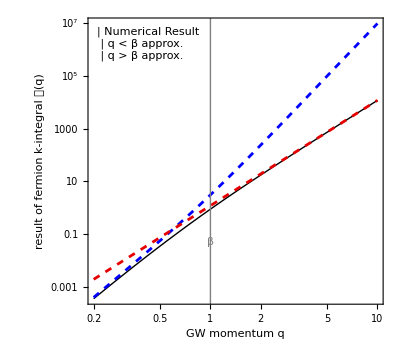

```mathematica
(* comparison between analytic and numerical result *)
RR={β->1};
Inum[qq_?NumericQ]:=NIntegrate[I1//.RR/.q->qq,{k,0,qq},{x,-1,1}];
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thickness[0.08],Black]],"Numerical Result"},
{LegendLine[Directive[Thick,Blue,Dashed]],"q < β approx."},
{LegendLine[Directive[Thick,RGBColor[.9,0,0],Dashed]],"q > β approx."}
},Spacings->{0.8},Alignment->{Left,Center}]];
LogLogPlot[{Inum[q],Klowq//.RR,Khighq//.RR},{q,0.2,10},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Dashed],Directive[RGBColor[.9,0,0],Dashed]},
FrameLabel->{"GW momentum q","result of fermion k-integral 𝒦(q)"},GridLines->Automatic,
Epilog->{Gray,Line[{{Log[β],-22},{Log[β],100}}//.RR],
Text["β",{Log[β]//.RR,-3},{-2,0}],
Black,Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}]
Export["~/Dropbox/nr-from-gw/K-q-approx.pdf",%];
```

```mathematica
(* now the q integral *)
$Assumptions=Union[$Assumptions,{n>0,m>0}];
(*Plowq=(6 H0^2)/q^5 Ωpeak(q/qpeak)^m;
Phighq=(6 H0^2)/q^5 Ωpeak(q/qpeak)^-n;*)
Plowq=(3 H0^2)/(2π q^5)Ωpeak(q/qpeak)^m;
Phighq=(3 H0^2)/(2π q^5)Ωpeak(q/qpeak)^-n;
Iqlow=Integrate[q^2 Plowq*Klowq,{q,0,qpeak}];
(*Iqlow=Integrate[q^2 Plowq*q^6 (3.0639818565657047+Log[β/q] (+1.2352092352092352 Log[β/q])),{q,0,qpeak}];*)
Iqhigh=Integrate[q^2 Phighq*Khighq,{q,qpeak,qmax}];
Iqhigh2=Integrate[q^2 Phighq*Khighq/.n->2,{q,qpeak,qmax}]
```

19/105 H0^2 π qpeak^2 β^2 Ωpeak Log[qmax/qpeak]

```mathematica
IqlowB=FullSimplify[Iqlow/(3 H0^2/(2π)/(4+m)*qpeak^4 Ωpeak)//.{
Log[qpeak^2]->2Log[qpeak],
Log[qpeak]->-Log[βoverq]+Log[β],
Log[x_*y_]:>Log[x]+Log[y],
a_ Log[x_]+a_ Log[y_]:>a Log[x*y],
a_ Log[x_]-a_ Log[y_]:>a Log[x/y]}];
(*FullSimplify[N[IqlowB]]
Collect[%,Log[βoverq]]*)
N[Series[Coefficient[IqlowB,Log[βoverq],0],{m,3,1}]]
N[Coefficient[IqlowB,Log[βoverq],1]]
N[Coefficient[IqlowB,Log[βoverq],2]]

(* including the prefactor in Subscript[C, coh] (and put back the numerical factors removed in the definition of IqlowB) *)
N[Series[Coefficient[IqlowB*1/(8π)*3/(2π),Log[βoverq],0],{m,3,1}]]
Expand[N[Coefficient[IqlowB*1/(8π)*3/(2π),Log[βoverq],1]]]
N[Coefficient[IqlowB*1/(8π)*3/(2π),Log[βoverq],2]]

(* simplifying the final expression for the PRL version *)
N[Iqlow*1/(8π)/.{m->3,β->qpeak}]
```

3.10339-0.0128324 (m-3.)+O[m-3.]^2

-0.0770479+2.47042/(4.+m)

1.23521

0.0589574-0.000243786 (m-3.)+O[m-3.]^2

-0.00146374+0.0469323/(4.+m)

0.0234662

0.00842248 H0^2 qpeak^4 Ωpeak

```mathematica
Simplify[Iqhigh/(3 H0^2/(2π)*qpeak^4 Ωpeak(β^2/qpeak^2))]
Simplify[Iqhigh2/(3 H0^2/(2π)*qpeak^4 Ωpeak(β^2/qpeak^2))]

(* including the prefactor in Subscript[C, coh] *)
N[Simplify[Iqhigh*1/(8π)/(H0^2*qpeak^4 Ωpeak(β^2/qpeak^2))]]
N[Simplify[Iqhigh2*1/(8π)/(H0^2*qpeak^4 Ωpeak(β^2/qpeak^2))]]
```

-(38 π^2 (qpeak^2-qmax^(2-n) qpeak^n))/(315 (2-n) qpeak^2)

38/315 π^2 Log[qmax/qpeak]

-(0.022619 (qpeak^2-1. qmax^(2.-1. n) qpeak^n))/((2.-1. n) qpeak^2)

0.022619 Log[qmax/qpeak]

#### Momentum integrals – coherent GWs – with exponential regulator (EXPERIMENTAL)

```mathematica
(* time integral *)
$Assumptions={ω>0,k>0,q>0,β>0,ϵ>0};
Integrate[1/τ(1-Exp[-π β τ])Exp[I(ω+k+q)τ(1+I ϵ)],{τ,0,∞}]
FullSimplify[%/.{-Log[x_]+Log[y_]:>Log[y/x]}]
```

-Log[(-ⅈ+ϵ) (k+q+ω)]+Log[π β+k (-ⅈ+ϵ)+q (-ⅈ+ϵ)-ⅈ ω+ϵ ω]

Log[1+(π β)/((-ⅈ+ϵ) (k+q+ω))]

```mathematica
(* low q, i.e. q<β -> neglect 1 in the logs; split off Log[±I] *)
$Assumptions={q>k>0,n>0,m>0,qmax>qpeak>qH>0,0<θ<π,ϵ>0,M>0};
I1=2 k^4(1-x^2)(k+ω)(2-(((ω+k)^2+q^2)(1-x^2))/(2ω(ω+k-q x)))Log[1-(I π β)/(ω+q+k)]Log[1+(I π β)/(ω+q+k)]/.ω->Sqrt[k^2+q^2-2k q x];
I2loq=2 k^4(1-x^2)(k+ω)(2-(((ω+k)^2+q^2)(1-x^2))/(2ω(ω+k-q x)))(π^2/4+Log[(π β)/(k+q+ω)]^2)/.ω->Sqrt[k^2+q^2-2k q x];
I3loq=Simplify[Integrate[I2loq,x]];
I4loq=Simplify[Limit[I3loq,x->1]-Limit[I3loq,x->-1]];

(* high-q - Azadeh's approach: expand logs around 1 *)
I2hiq=2 k^4(1-x^2)(k+ω)(2-(((ω+k)^2+q^2)(1-x^2))/(2ω(ω+k-q x)))((π β)/(ω+q+k))^2/.ω->Sqrt[k^2+q^2-2k q x];
I4hiq=Integrate[I2hiq,{x,-1,1},GenerateConditions->False];
```

```mathematica
I2hiq
```

(2 k^4 π^2 (1-x^2) (k+√(k^2+q^2-2 k q x)) (2-((1-x^2) (q^2+(k+√(k^2+q^2-2 k q x))^2))/(2 √(k^2+q^2-2 k q x) (k-q x+√(k^2+q^2-2 k q x)))) β^2)/((k+q+√(k^2+q^2-2 k q x))^2)

```mathematica
Series[I2hiq,{k,∞,0}]
Integrate[%,{x,-1,1}]

Series[Integrate[I2hiq,{x,-1,1}],{k,∞,0}]
```

-π^2 (-1+x^2) (1+x^2) β^2 k^3-1/2 (π^2 (-1+x^2) (-2 q-q x-2 q x^2+3 q x^3) β^2) k^2-1/2 (π^2 (-1+x^2) (q^2-2 q^2 x^2-4 q^2 x^3+5 q^2 x^4) β^2) k-5/8 (π^2 (-1+x^2) (q^3 x+2 q^3 x^2-4 q^3 x^3-6 q^3 x^4+7 q^3 x^5) β^2)+O[1/k]^1

2/105 π^2 (84 k^3-84 k^2 q+36 k q^2-5 q^3) β^2

-(4 (π^2 β^2) k^8)/(35 q^5)+(32 π^2 β^2 k^7)/(105 q^4)-(4 (π^2 β^2) k^6)/(15 q^3)+(2 π^2 β^2 k^4)/(3 q)+O[1/k]^1

(2 k^4 π^2 (-6 k^4+16 k^3 q-14 k^2 q^2+35 q^4) β^2)/(105 q^5)

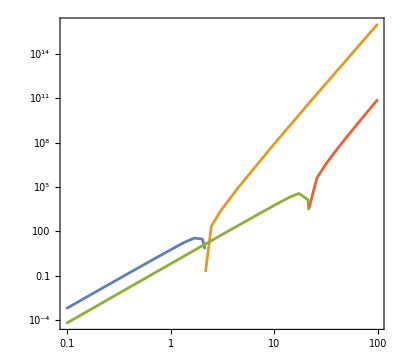

```mathematica
I4hiq
LogLogPlot[{I4hiq/.{β->1,q->1},-I4hiq/.{β->1,q->1},I4hiq/.{β->1,q->10},-I4hiq/.{β->1,q->10}},{k,0,100},PlotPoints->10,MaxRecursion->2,GridLines->Automatic]
```

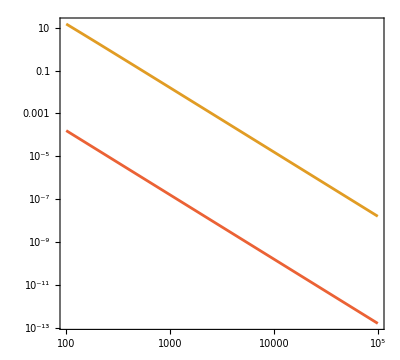

```mathematica
Clear[I5];
I5[ϵ_?NumericQ,qq_?NumericQ]:=NIntegrate[Exp[-k ϵ]I4hiq/.{β->1,q->qq},{k,0,∞}]
LogLogPlot[Evaluate[1/q^2{-I5[0.1,q],I5[0.1,q],-I5[1,q],I5[1,q]}],{q,100,100000},PlotPoints->10,MaxRecursion->2,GridLines->Automatic]
```

```mathematica
NIntegrate[q^2(1/q^2-1/(q^2-10^2))I5[.01,q],{q,1,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in q near {q} = {9.84766}. NIntegrate obtained -1.15621×10^22 and 9.29648×10^18 for the integral and error estimates.

-1.15621×10^22

```mathematica
I5b=Integrate[(1/q^2-1/(q^2-M^2))#,q]&/@List@@I4
```

```mathematica
I6b=List@@Collect[Total[I5b],k];
```

```mathematica
Limit[#,q->∞]&/@I6b
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

General::stop: Further output of Limit::alimv will be suppressed during this calculation.

$Aborted

```mathematica
Expand[Total[I5b]][[29]]
Expand[Total[I5b]][[30]]
```

-(1429 k^4 Log[q])/2835

-(1597129 k^10 Log[q])/(31255875 M^6)

```mathematica
Simplify[Total[I5b]]
```

```mathematica
Limit[#,q->∞]&/@List@@Expand[%][[1;;30]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

General::stop: Further output of Limit::alimv will be suppressed during this calculation.

{(16 k^4)/315,-(16 k^6)/(315 M^2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,k ∞,-(16 ⅈ k^9 π)/(1575 M^5),(19 ⅈ k^7 π)/(243 M^3),-(222248 ⅈ k^5 π)/(496125 M),-(18197 ⅈ k^3 M π)/99225,(29 ⅈ k M^3 π)/1575,-(2 ⅈ k^5 π^3)/(5 M),k^4 (-∞),k^10 (-∞)}

```mathematica
(*I5=Integrate[# Exp[-k ϵ],{k,qH,∞},GenerateConditions->False]&/@List@@I4*)
I5=Integrate[# Exp[-k ϵ],k,GenerateConditions->False]&/@List@@I4;
```

```mathematica
(*I7=Limit[#,k->∞]-(#/.k->0)&/@I6*)
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

General::stop: Further output of Limit::alimv will be suppressed during this calculation.

```mathematica
I6=Series[Total[I5],{ϵ,0,0}]⟦3⟧;
```

```mathematica
I7=Limit[#,k->∞]&/@I6;
```

```mathematica
I5a=Integrate[# Exp[-k ϵ],{k,0,∞},GenerateConditions->False]&/@List@@Collect[I4,k];
```

```mathematica
Integrate[ⅇ^(-k ϵ) k^4 Log[1/(k+1)]^2,{k,0,∞},GenerateConditions->False]
```

-1/(1728 ϵ^4)(2280 ϵ^4+2252 ϵ^5+900 ϵ^6+415 ϵ^7+216 ⅇ^ϵ Gamma[5,ϵ]-444 ⅇ^ϵ ϵ Gamma[5,ϵ]+460 ⅇ^ϵ ϵ^2 Gamma[5,ϵ]-415 ⅇ^ϵ ϵ^3 Gamma[5,ϵ]-864 ⅇ^ϵ MeijerG[{{},{1,1}},{{0,0,5},{}},ϵ]+1008 ⅇ^ϵ MeijerG[{{},{2,2}},{{1,1,6},{}},ϵ]-624 ⅇ^ϵ MeijerG[{{},{3,3}},{{2,2,7},{}},ϵ]+300 ⅇ^ϵ MeijerG[{{},{4,4}},{{3,3,8},{}},ϵ]-3456 ⅇ^ϵ MeijerG[{{},{0,0,0}},{{-1,-1,-1,4},{}},ϵ]+3456 ⅇ^ϵ MeijerG[{{},{1,1,1}},{{0,0,0,5},{}},ϵ]-1728 ⅇ^ϵ MeijerG[{{},{2,2,2}},{{1,1,1,6},{}},ϵ]+576 ⅇ^ϵ MeijerG[{{},{3,3,3}},{{2,2,2,7},{}},ϵ]-144 ⅇ^ϵ MeijerG[{{},{4,4,4}},{{3,3,3,8},{}},ϵ])

```mathematica
TT=Integrate[ⅇ^(-k ϵ) k^4 (8/3 q Log[(π β)/(2 (k+q))]^2),k,GenerateConditions->False];
SS=Series[TT,{ϵ,0,0}]
```

-1/(3 ϵ^5)32 (q (-25 Log[k+q]+12 EulerGamma Log[k+q]+6 Log[k+q]^2-25 Log[(π β)/(2 (k+q))]+12 EulerGamma Log[(π β)/(2 (k+q))]+12 Log[k+q] Log[(π β)/(2 (k+q))]+6 Log[(π β)/(2 (k+q))]^2+12 Log[k+q] Log[ϵ]+12 Log[(π β)/(2 (k+q))] Log[ϵ]))+(32 q (q Log[k+q]+q Log[(π β)/(2 (k+q))]))/ϵ^4-(16 (q (q^2 Log[k+q]+q^2 Log[(π β)/(2 (k+q))])))/(3 ϵ^3)+(16 q (q^3 Log[k+q]+q^3 Log[(π β)/(2 (k+q))]))/(9 ϵ^2)-(4 (q (q^4 Log[k+q]+q^4 Log[(π β)/(2 (k+q))])))/(3 ϵ)-1/3375 q (-144 k^5+405 k^4 q-940 k^3 q^2+2310 k^2 q^3-8220 k q^4-12019 q^5+7500 q^5 Log[k+q]+3600 EulerGamma q^5 Log[k+q]+1800 q^5 Log[k+q]^2-720 k^5 Log[(π β)/(2 (k+q))]+900 k^4 q Log[(π β)/(2 (k+q))]-1200 k^3 q^2 Log[(π β)/(2 (k+q))]+1800 k^2 q^3 Log[(π β)/(2 (k+q))]-3600 k q^4 Log[(π β)/(2 (k+q))]-720 q^5 Log[(π β)/(2 (k+q))]+3600 EulerGamma q^5 Log[(π β)/(2 (k+q))]+3600 q^5 Log[k+q] Log[(π β)/(2 (k+q))]-1800 k^5 Log[(π β)/(2 (k+q))]^2+3600 q^5 Log[k+q] Log[ϵ]+3600 q^5 Log[(π β)/(2 (k+q))] Log[ϵ])+O[ϵ]^1

```mathematica
FullSimplify[SS⟦3,-1⟧]
```

1/3375 q ((k+q) (144 k^4-549 k^3 q+1489 k^2 q^2-3799 k q^3+12019 q^4)-1800 q^5 Log[k+q]^2-300 q^5 Log[k+q] (25+12 Log[(π β)/(2 (k+q))])+60 Log[(π β)/(2 (k+q))] (12 k^5-15 k^4 q+20 k^3 q^2-30 k^2 q^3+60 k q^4+12 q^5+30 k^5 Log[(π β)/(2 (k+q))])-3600 q^5 Log[(π β)/2] (EulerGamma+Log[ϵ]))

```mathematica
Limit[SS⟦3,-1⟧,k->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

q ∞

```mathematica
SS[[3]]
```

{-32/3 q (-25 Log[k+q]+12 EulerGamma Log[k+q]+6 Log[k+q]^2-25 Log[(π β)/(2 (k+q))]+12 EulerGamma Log[(π β)/(2 (k+q))]+12 Log[k+q] Log[(π β)/(2 (k+q))]+6 Log[(π β)/(2 (k+q))]^2+12 Log[k+q] Log[ϵ]+12 Log[(π β)/(2 (k+q))] Log[ϵ]),32 q (q Log[k+q]+q Log[(π β)/(2 (k+q))]),-16/3 q (q^2 Log[k+q]+q^2 Log[(π β)/(2 (k+q))]),16/9 q (q^3 Log[k+q]+q^3 Log[(π β)/(2 (k+q))]),-4/3 q (q^4 Log[k+q]+q^4 Log[(π β)/(2 (k+q))]),-1/3375 q (-144 k^5+405 k^4 q-940 k^3 q^2+2310 k^2 q^3-8220 k q^4-12019 q^5+7500 q^5 Log[k+q]+3600 EulerGamma q^5 Log[k+q]+1800 q^5 Log[k+q]^2-720 k^5 Log[(π β)/(2 (k+q))]+900 k^4 q Log[(π β)/(2 (k+q))]-1200 k^3 q^2 Log[(π β)/(2 (k+q))]+1800 k^2 q^3 Log[(π β)/(2 (k+q))]-3600 k q^4 Log[(π β)/(2 (k+q))]-720 q^5 Log[(π β)/(2 (k+q))]+3600 EulerGamma q^5 Log[(π β)/(2 (k+q))]+3600 q^5 Log[k+q] Log[(π β)/(2 (k+q))]-1800 k^5 Log[(π β)/(2 (k+q))]^2+3600 q^5 Log[k+q] Log[ϵ]+3600 q^5 Log[(π β)/(2 (k+q))] Log[ϵ])}

```mathematica
Limit[#,k->∞]&/@SS⟦3,-1⟧
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

General::stop: Further output of Limit::alimv will be suppressed during this calculation.

{-32/3 q Log[(π β)/2] (-25+12 EulerGamma-6 Log[2]+6 Log[π]+6 Log[β]+12 Log[ϵ]),32 q^2 Log[(π β)/2],-16/3 q^3 Log[(π β)/2],16/9 q^4 Log[(π β)/2],-4/3 q^5 Log[(π β)/2],q ∞}

```mathematica
$Assumptions=Union[$Assumptions,{n>0,m>0,qpeak>0,Ωpeak>0}];
Plowq=(3 H0^2)/(2π q^5)Ωpeak(q/qpeak)^m;
Phighq=(3 H0^2)/(2π q^5)Ωpeak(q/qpeak)^-n;
Iqlow=Integrate[q^2 Plowq*I7,{q,0,qpeak}];
(*(*Iqlow=Integrate[q^2 Plowq*q^6 (3.0639818565657047+Log[β/q] (+1.2352092352092352 Log[β/q])),{q,0,qpeak}];*)
Iqhigh=Integrate[q^2 Phighq*Khighq,{q,qpeak,qmax}];
Iqhigh2=Integrate[q^2 Phighq*Khighq/.n->2,{q,qpeak,qmax}]
*)
```

```mathematica
I6=Flatten[List@@Expand[#]&/@I5];
```

```mathematica
I7=I6/.{Integrate[___]:>0};
```

Integrate::argmu: Integrate called with 1 argument; 2 or more arguments are expected.

```mathematica
Series[I8,{ϵ,0,0}]
```

-(512 (-82633+32540 EulerGamma+6300 π^2+32540 Log[q]+32540 Log[(π β)/(2 q)]+32540 Log[ϵ]))/(35 q^5 ϵ^11)+1924096/(35 q^4 ϵ^10)+(64 (-21199+8636 EulerGamma+1260 π^2+8636 Log[q]+8636 Log[(π β)/(2 q)]+8636 Log[ϵ]))/(35 q^3 ϵ^9)-(64 (1629+980 EulerGamma+980 Log[q]+980 Log[(π β)/(2 q)]+980 Log[ϵ]))/(105 q^2 ϵ^8)-(96 (-99+28 EulerGamma-70 π^2+28 Log[q]+28 Log[(π β)/(2 q)]+28 Log[ϵ]))/(35 q ϵ^7)+1/(525 ϵ^6)32 (-5084+2950 EulerGamma+1575 π^2-25820 Log[q]+12600 EulerGamma Log[q]+6300 Log[q]^2-25820 Log[(π β)/(2 q)]+12600 EulerGamma Log[(π β)/(2 q)]+12600 Log[q] Log[(π β)/(2 q)]+6300 Log[(π β)/(2 q)]^2+2950 Log[ϵ]+12600 Log[q] Log[ϵ]+12600 Log[(π β)/(2 q)] Log[ϵ])+1/(315 ϵ^5)8 (-4343 q+1856 EulerGamma q+630 π^2 q-14692 q Log[q]+5040 EulerGamma q Log[q]+2520 q Log[q]^2-15364 q Log[(π β)/(2 q)]+5040 EulerGamma q Log[(π β)/(2 q)]+5040 q Log[q] Log[(π β)/(2 q)]+2520 q Log[(π β)/(2 q)]^2+1856 q Log[ϵ]+5040 q Log[q] Log[ϵ]+5040 q Log[(π β)/(2 q)] Log[ϵ])+1/(128625 ϵ^4)8 (-277689 q^2+104020 EulerGamma q^2-317380 q^2 Log[q]+117600 EulerGamma q^2 Log[q]+58800 q^2 Log[q]^2-426300 q^2 Log[(π β)/(2 q)]+117600 EulerGamma q^2 Log[(π β)/(2 q)]+117600 q^2 Log[q] Log[(π β)/(2 q)]+104020 q^2 Log[ϵ]+117600 q^2 Log[q] Log[ϵ]+117600 q^2 Log[(π β)/(2 q)] Log[ϵ])+(2 (-1811 q^3+760 EulerGamma q^3-320 q^3 Log[q]-920 q^3 Log[(π β)/(2 q)]+760 q^3 Log[ϵ]))/(1575 ϵ^3)+1/(31255875 ϵ^2)2 (-6336649 q^4+1646820 EulerGamma q^4+6806520 q^4 Log[q]+1587600 EulerGamma q^4 Log[q]+793800 q^4 Log[q]^2+5159700 q^4 Log[(π β)/(2 q)]+1587600 EulerGamma q^4 Log[(π β)/(2 q)]+1587600 q^4 Log[q] Log[(π β)/(2 q)]+1646820 q^4 Log[ϵ]+1587600 q^4 Log[q] Log[ϵ]+1587600 q^4 Log[(π β)/(2 q)] Log[ϵ])+(-3024000+8416 q^5-111360 EulerGamma q^5-1486080 q^5 Log[q]-1414335 q^5 Log[(π β)/(2 q)]-111360 q^5 Log[ϵ])/(3024000 ϵ)+1/(69155856000 q^5)(-69155856000-69155856000 q^2-69155856000 q^4-150797842965 q^5-69155856000 q^10+99538323488 q^11-1659651840 EulerGamma q^11-58565041920 q^11 Log[q]-24588748800 EulerGamma q^11 Log[q]-12294374400 q^11 Log[q]^2-69155856000 q^5 Log[(π β)/(2 q)]+4566481920 q^11 Log[(π β)/(2 q)]-24588748800 EulerGamma q^11 Log[(π β)/(2 q)]-24588748800 q^11 Log[q] Log[(π β)/(2 q)]-1659651840 q^11 Log[ϵ]-24588748800 q^11 Log[q] Log[ϵ]-24588748800 q^11 Log[(π β)/(2 q)] Log[ϵ])+O[ϵ]^1

```mathematica
I8=Simplify[Total[-(#/.k->0)&/@I7]];
I9=Limit[I8,q->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

```mathematica
Limit[I8,ϵ->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Indeterminate

```mathematica
I5//.{
Log[q^2]->2Log[q],
Log[q]->-Log[πβ2q]+Log[π]+Log[β]-Log[2],
a_ Log[x_]+a_ Log[y_]:>a Log[x*y],
a_ Log[x_]-a_ Log[y_]:>a Log[x/y]};
Simplify[Expand[%]]
FullSimplify[N[%]]
```

1/166406278500 q^6 (86500816519+51386643000 π^2-339352758360 Log[2]+906325912800 Log[2]^2+125365002840 Log[π]-878279371200 Log[2] Log[π]+205546572000 Log[π]^2-27720 (-4522547+31683960 Log[2]-14830200 Log[π]) Log[β/q]+205546572000 Log[β/q]^2)

q^6 (3.06398+Log[β/q] (-0.0770479+1.23521 Log[β/q]))

### Prefactors for phenomenological scaling relations

```mathematica
(* Subscript[Ω, ψ,0] in sec. 6 *)
π^2/270 106.75^(4/3)/3.38^(1/3)100^4((3*^11GeV)^5)/(2.73Kelvin)(1*^-6)/(1/(8π GN)^2)//.NN
```

0.362124

```mathematica
(* Subscript[q, peak] in sec. 6 *)
100(T0 3.38^(1/3))/(T*106.75^(1/3))*Sqrt[(8π GN)/3 π^2/30]Sqrt[106.75] T^2/.T->3*^11GeV/Hz//.NN
```

### Evaluation of G_1

```mathematica
(* in the following, we define k along the z-axis, and q in direction (θ,ϕ) *)
$Assumptions={(#∈Reals&)/@{ω,k,k1,k2,k3,q},ω>0,k>0,k3>0,k^2>=k1^2+k2^2+k3^2,0<θ<π,0<ϕ<2π};
σ=Table[PauliMatrix[j],{j,0,3}];
σbar={1,-1,-1,-1}*σ;
ϕhat={-Sin[ϕ],Cos[ϕ],0};
θhat=-FullSimplify[Cross[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},ϕhat]];
ep=1/Sqrt[2](θhat+I ϕhat);
em=1/Sqrt[2](θhat-I ϕhat);
Xp=Sqrt[2]Sum[PauliMatrix[j]*ep⟦j⟧,{j,1,3}]*ep.{0,0,1};
Xm=Sqrt[2]Sum[PauliMatrix[j]*em⟦j⟧,{j,1,3}]*em.{0,0,1};
Ep=(Sum[{k,k1,k2,k3}⟦j⟧*σ⟦j⟧,{j,1,4}]/Sqrt[2k(k+k3)]).{1,0}; (* Subscript[E, k]^+ *)
Em=(Sum[{k,k1,k2,k3}⟦j⟧*σbar⟦j⟧,{j,1,4}]/Sqrt[2k(k+k3)]).{0,1}; (* Subscript[E, k]^– *)
Epkq=Ep/.{k->ω,k1->k1-q Sin[θ]Cos[ϕ],k2->k2-q Sin[θ]Sin[ϕ],k3->k3-q Cos[θ]}; (* Subscript[E, k-q]^+ *)
Emkq=Em/.{k->ω,k1->k1-q Sin[θ]Cos[ϕ],k2->k2-q Sin[θ]Sin[ϕ],k3->k3-q Cos[θ]}; (* Subscript[E, k-q]^+ *)
XEpp=((ω+k+q)Sin[θ])/(2Sqrt[ω(ω+k-q Cos[θ])]){Sin[θ],Exp[I ϕ](1-Cos[θ])}; (* direct implementation of the X.E products *)
XEmp=((ω+k-q)Sin[θ])/(2Sqrt[ω(ω+k-q Cos[θ])]){Sin[θ],-Exp[I ϕ](1+Cos[θ])};
XEpm=-((ω+k-q)Sin[θ])/(2Sqrt[ω(ω+k-q Cos[θ])]){Exp[-I ϕ](1+Cos[θ]),Sin[θ]};
XEmm=((ω+k+q)Sin[θ])/(2Sqrt[ω(ω+k-q Cos[θ])]){Exp[-I ϕ](1-Cos[θ]),-Sin[θ]};
```

```mathematica
(* the following should reproduce eqs. 3.16–3.19 *)
FullSimplify[Xp.Epkq]/.{k1->0,k2->0,k3->k}
FullSimplify[Xm.Epkq]/.{k1->0,k2->0,k3->k}
FullSimplify[Xp.Emkq]/.{k1->0,k2->0,k3->k}
FullSimplify[Xm.Emkq]/.{k1->0,k2->0,k3->k}
```

{((k+q+ω) Sin[θ]^2)/(2 √(ω (k+ω-q Cos[θ]))),-(ⅇ^(ⅈ ϕ) (k+q+ω) (-1+Cos[θ]) Sin[θ])/(2 √(ω (k+ω-q Cos[θ])))}

{((k-q+ω) Sin[θ]^2)/(2 √(ω (k+ω-q Cos[θ]))),-(ⅇ^(ⅈ ϕ) (k-q+ω) (1+Cos[θ]) Sin[θ])/(2 √(ω (k+ω-q Cos[θ])))}

{-(ⅇ^(-ⅈ ϕ) (k-q+ω) (1+Cos[θ]) Sin[θ])/(2 √(ω (k+ω-q Cos[θ]))),-((k-q+ω) Sin[θ]^2)/(2 √(ω (k+ω-q Cos[θ])))}

{-(ⅇ^(-ⅈ ϕ) (k+q+ω) (-1+Cos[θ]) Sin[θ])/(2 √(ω (k+ω-q Cos[θ]))),-((k+q+ω) Sin[θ]^2)/(2 √(ω (k+ω-q Cos[θ])))}

```mathematica
reps={k1->0,k2->0,k3->k(*,ω->Sqrt[k^2+q^2-2k q Cos[θ]]*)};
Cm=Simplify[ComplexExpand[(Conjugate[Ep].XEpm)(Conjugate[XEpm].Ep)]
+ComplexExpand[(Conjugate[Ep].XEmm)(Conjugate[XEmm].Ep)]//.reps];
Cp=Simplify[ComplexExpand[(Conjugate[Em].XEpp)(Conjugate[XEpp].Em)]
+ComplexExpand[(Conjugate[Em].XEmp)(Conjugate[XEmp].Em)]//.reps];
Simplify[Cm-Cp] (* verify that the two expressions are identical *)

(* Azadeh's expressions *)
CmA=2 Sin[θ]^2-1/2((ω+k)^2+q^2)/(ω(ω+k-q Cos[θ]))Sin[θ]^4//.reps;
CpA=CmA;
```

0

```mathematica
FullSimplify[Cm-CmA/.ω->Sqrt[k^2+q^2-2k q Cos[θ]],Assumptions->Union[$Assumptions,{k+ω-q Cos[θ]>0}]]
```

0

```mathematica
{Simplify[Cm],Simplify[CmA]}//.{k->2,ω->Sqrt[k^2+q^2-2k q Cos[θ]],q->3,θ->π/7.}
```

{0.0508904,0.0508904}